```mathematica
a=0.9;
```

```mathematica
g[x_,y_]:=Piecewise[{{(Cos[π x/2]+Cos[π y/2])ⅇ^-a,Abs[x]<1&&Abs[y]<1},{(Cos[π x/2])ⅇ^(-a Abs[y]),Abs[x]<1&&Abs[y]>1},{(Cos[π y/2])ⅇ^(-a Abs[x]),Abs[x]>1&&Abs[y]<1}}]
```

```mathematica
Plot3D[g[x,y],{x,-4,4},{y,-4,4},PlotRange->Full]
```

-Graphics3D-

```mathematica
j[x_]:=g[x,0.5]
```

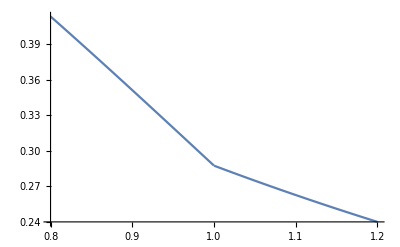

```mathematica
Plot[j[x],{x,0.8,1.2}]
```